```mathematica
kern[α_,β_,t_]:=α β ⅇ^(-β t);
```

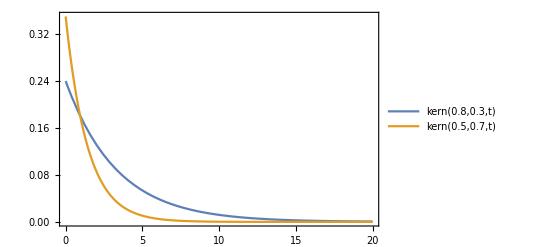

```mathematica
Plot[{kern[0.8,0.3,t],kern[0.5,0.7,t]},{t,0,20},Frame->True,PlotRange->All,PlotLegends->"Expressions"]
```

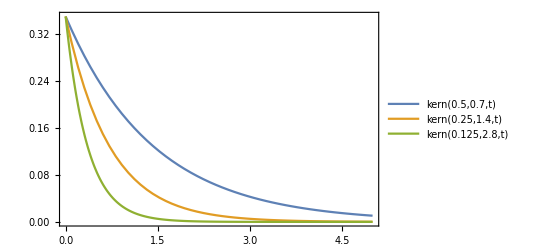

```mathematica
Plot[{kern[0.5,0.7,t],kern[0.25,1.4,t],kern[0.125,2.8,t]},{t,0,5},Frame->True,PlotRange->All,PlotLegends->"Expressions"]
```

```mathematica
Plot3D[kern[1,β,t],{β,0,10},{t,0.00001,1},PlotRange->All,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[kern[0.1,β,t],{β,0,10},{t,0.00001,1},PlotRange->All,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[kern[0.1,β,t],{β,0,100},{t,0.00001,0.1},PlotRange->All,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[kern[0.1,β,t],{β,0,1000},{t,0.00001,0.01},PlotRange->All,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[kern[0.1,β,t],{β,0,100000},{t,0.00001,0.0001},PlotRange->All,AxesLabel->Automatic, ImageSize-> Large]
```

-Graphics3D-

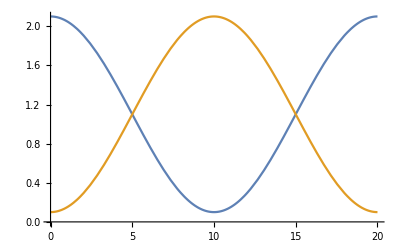

```mathematica
Plot[{Cos[π t/10]+1.1,Cos[π (t/10+1)]+1.1},{t,0,20}]
```

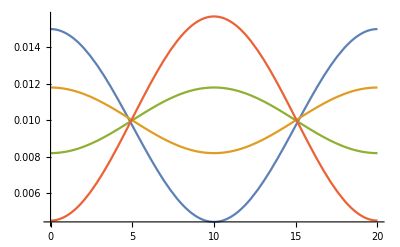

```mathematica
Plot[{0.007061(Cos[π t/10]+1.1)+0.001771(Cos[π (t/10+1)]+1.1),
0.005445(Cos[π t/10]+1.1)+0.003645(Cos[π (t/10+1)]+1.1),
0.003645(Cos[π t/10]+1.1)+0.005445(Cos[π (t/10+1)]+1.1),0.001790(Cos[π t/10]+1.1)+0.007390(Cos[π (t/10+1)]+1.1)},{t,0,20}]
```

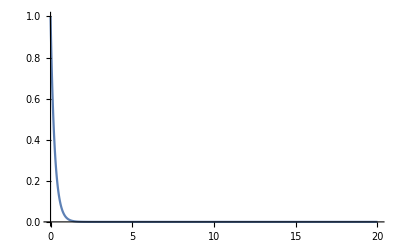

```mathematica
Plot[{Exp[-4t]},{t,0,20},PlotRange->All]
```

```mathematica
kerneldiscretization = Join[
Range[0.0,0.01-0.001, 0.001],
Range[0.01,0.1-0.01, 0.01],
Range[0.1,1.-0.1, 0.1],
Range[1.,5., 0.25]]
```

{0.,0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.}

```mathematica
kerneldiscretization2 = Join[
{0, 0.000025,0.000075},
Range[0.001,0.01-0.001, 0.001],
Range[0.01,0.1-0.01, 0.01],
Range[0.1,1.-0.1, 0.1],
Range[1.,5., 0.25]]
```

{0,0.000025,0.000075,0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.}

```mathematica
kerneldiscretization3 = {0.,0.000025,0.00075,0.001,0.002,0.005,0.01,0.02,0.05,0.1,0.2,0.5,1.0,2.0,5.0}
```

{0.,0.000025,0.00075,0.001,0.002,0.005,0.01,0.02,0.05,0.1,0.2,0.5,1.,2.,5.}

```mathematica
kernlat[α_,β_,t_,t0_]:=If[t≥t0,α β ⅇ^(-β (t-t0)),0];
```

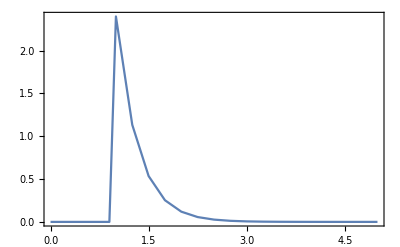

```mathematica
ListLinePlot[Map[{#,kernlat[0.8,3,#,1]}&,kerneldiscretization2],Frame->True,PlotRange->All]
```

General::munfl: Exp[-799.975] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-899.975] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-999.975] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

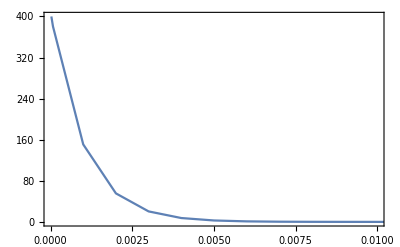

```mathematica
ListLinePlot[Map[{#,kernlat[0.4,1000,#,0.000025]}&,Rest[kerneldiscretization2]],Frame->True,PlotRange->{{0, 0.01},All}]
```

```mathematica
ListLinePlot[Map[{#,kernlat[0.8,3,#,0.1]+kernlat[0.4,1000,#,0.000025]}&,Rest[kerneldiscretization2]],Frame->True,PlotRange->{{0, 0.01},All}]
```

General::munfl: Exp[-799.975] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-899.975] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-999.975] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

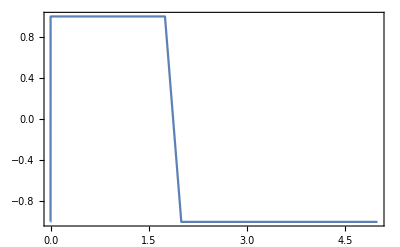

```mathematica
ListLinePlot[Map[{#,Sign[kernlat[0.8,3,#,0.001]-0.01]}&,Rest[kerneldiscretization2]],Frame->True,PlotRange->{{0, 5},All}]
```

General::munfl: Exp[-799.975] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-899.975] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-999.975] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

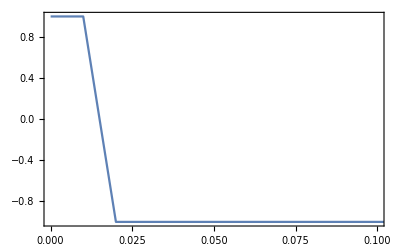

```mathematica
ListLinePlot[Map[{#,Sign[kernlat[0.4,1000,#,0.000025]-0.01]}&,Rest[kerneldiscretization2]],Frame->True,PlotRange->{{0, 0.1},All}]
```

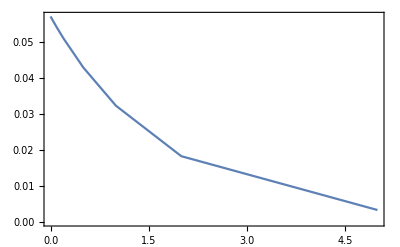
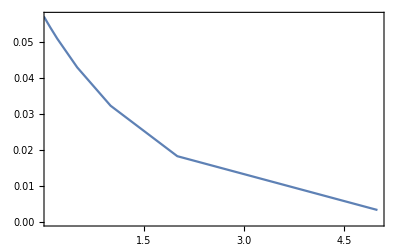

```mathematica
{ListLinePlot[Map[{#,kernlat[0.1,0.57,#,0.000025]}&,Rest[kerneldiscretization3]],Frame->True,PlotRange->{{0,5},Automatic}],
ListLinePlot[Map[{#,kernlat[0.1,0.57,#,0.000025]}&,Rest[kerneldiscretization3]],Frame->True,PlotRange->{{0.1,5},Automatic}]}
```

```mathematica
Map[{#,kernlat[0.1,0.57,#,0.000025]}&,Rest[kerneldiscretization3]]
```

{{0.000025,0.057},{0.00075,0.0569764},{0.001,0.0569683},{0.002,0.0569359},{0.005,0.0568386},{0.01,0.0566768},{0.02,0.0563547},{0.05,0.0553992},{0.1,0.0538426},{0.2,0.0508594},{0.5,0.0428654},{1.,0.0322354},{2.,0.0182299},{5.,0.00329717}}

General::munfl: Exp[-759.281] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1518.58] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3796.48] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

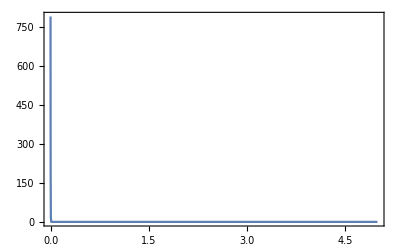
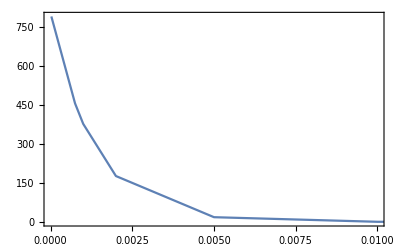

```mathematica
{ListLinePlot[Map[{#,kernlat[1.04,759.3,#,0.000025]}&,Rest[kerneldiscretization3]],Frame->True,PlotRange->{{0,5},Automatic}],
ListLinePlot[Map[{#,kernlat[1.04,759.3,#,0.000025]}&,Rest[kerneldiscretization3]],Frame->True,PlotRange->{{0,0.01},Automatic}]}
```

```mathematica
{Grid[Map[{#,kernlat[0.1,0.57,#,0.000025]}&,Rest[kerneldiscretization3]],Frame->True],
Grid[Map[{#,kernlat[1.04,759.3,#,0.000025]}&,Rest[kerneldiscretization3]],Frame->True]}
```

General::munfl: Exp[-759.281] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1518.58] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3796.48] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.000025 | 0.057
0.00075 | 0.0569764
0.001 | 0.0569683
0.002 | 0.0569359
0.005 | 0.0568386
0.01 | 0.0566768
0.02 | 0.0563547
0.05 | 0.0553992
0.1 | 0.0538426
0.2 | 0.0508594
0.5 | 0.0428654
1. | 0.0322354
2. | 0.0182299
5. | 0.00329717,0.000025 | 789.672
0.00075 | 455.377
0.001 | 376.644
0.002 | 176.267
0.005 | 18.0672
0.01 | 0.405595
0.02 | 0.000204407
0.05 | 2.61638×10^-14
0.1 | 8.50571×10^-31
0.2 | 8.9894×10^-64
0.5 | 1.06118×10^-162
1. | 0.
2. | 0.
5. | 0.}

```mathematica
{Grid[Map[{#,kernlat[0.1,0.57,#,0.000025]}&,Rest[kerneldiscretization3]],Frame->True],
Grid[Map[{#,kernlat[1.04,759.3,#,0.000025]}&,Rest[kerneldiscretization3]],Frame->True]}
```

```mathematica
Grid[Table[{t,kern[0.5,0.7,t]},{t,0,3.75,0.25}],Frame->All]
```

0. | 0.35
0.25 | 0.29381
0.5 | 0.246641
0.75 | 0.207044
1. | 0.173805
1.25 | 0.145902
1.5 | 0.122478
1.75 | 0.102815
2. | 0.0863089
2.25 | 0.0724526
2.5 | 0.0608209
2.75 | 0.0510565
3. | 0.0428597
3.25 | 0.0359789
3.5 | 0.0302028
3.75 | 0.0253539

```mathematica
{Grid[Map[{#,kernlat[0.21,3.4,#,0.00000001]}&,Rest[kerneldiscretization3]],Frame->True],
Grid[Map[{#,kernlat[3.49,6093.9,#,0.00000001]}&,Rest[kerneldiscretization3]],Frame->True]}
```

General::munfl: Exp[-1218.78] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3046.95] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6093.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.000025 | 0.713939
0.00075 | 0.712182
0.001 | 0.711577
0.002 | 0.709161
0.005 | 0.701965
0.01 | 0.690132
0.02 | 0.667062
0.05 | 0.602377
0.1 | 0.508204
0.2 | 0.361725
0.5 | 0.130436
1. | 0.0238285
2. | 0.000795235
5. | 2.95592×10^-8,0.000025 | 18263.5
0.00075 | 220.21
0.001 | 47.9955
0.002 | 0.108306
0.005 | 1.24455×10^-9
0.01 | 7.28242×10^-23
0.02 | 2.49347×10^-49
0.05 | 1.0009×10^-128
0.1 | 4.71013×10^-261
0.2 | 0.
0.5 | 0.
1. | 0.
2. | 0.
5. | 0.}